```mathematica
;
```

Last updated:   Sat 4 Jun 2022

## About Jazz

```mathematica
(* set text style *)
;
extractInfo[items_List]:=
```

```mathematica
(* summary of Wikipedia article *)
```

Jazz is a music genre that originated in the African-American communities of New Orleans, Louisiana in the late 19th and early 20th centuries, with its roots in blues and ragtime. Since the 1920s Jazz Age, it has been recognized as a major form of musical expression in traditional and popular music. Jazz is characterized by swing and blue notes, complex chords, call and response vocals, polyrhythms and improvisation. Jazz has roots in European harmony and African rhythmic rituals.As jazz spread around the world, it drew on national, regional, and local musical cultures, which gave rise to different styles. New Orleans jazz began in the early 1910s, combining earlier brass-band marches, French quadrilles, biguine, ragtime and blues with collective polyphonic improvisation. But jazz didn't begin as a single musical tradition in New Orleans or elsewhere. In the 1930s, arranged dance-oriented swing big bands, Kansas City jazz (a hard-swinging, bluesy, improvisational style), and gypsy jazz (a style that emphasized musette waltzes) were the prominent styles. Bebop emerged in the 1940s, shifting jazz from danceable popular music toward a more challenging "musician's music" which was played at faster tempos and used more chord-based improvisation. Cool jazz developed near the end of the 1940s, introducing calmer, smoother sounds and long, linear melodic lines.The mid-1950s saw the emergence of hard bop, which introduced influences from rhythm and blues, gospel, and blues, especially in the saxophone and piano playing. Modal jazz developed in the late 1950s, using the mode, or musical scale, as the basis of musical structure and improvisation, as did free jazz, which explored playing without regular meter, beat and formal structures. Jazz-rock fusion appeared in the late 1960s and early 1970s, combining jazz improvisation with rock music's rhythms, electric instruments, and highly amplified stage sound. In the early 1980s, a commercial form of jazz fusion called smooth jazz became successful, garnering significant radio airplay. Other styles and genres abound in the 2000s, such as Latin and Afro-Cuban jazz.

```mathematica
(* some properties of Wikidata entry *)
```

Dataset[<>]

```mathematica
(* clean text (lower case -> delete stopwords -> remove diacritics) -> plot word cloud *)
:=;
```

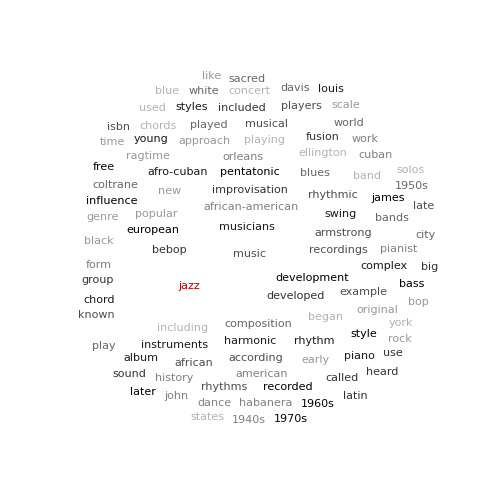
-Graphics- |  —  — jazz400
 —  — music129
 —  — new84
 —  — musicians74
 —  — blues50
 —  — band43
 —  — bebop38
 —  — orleans37
 —  — style36
 —  — early33
 —  — african33
 —  — swing32
 —  — fusion29
 —  — began29
 —  — bands29
 —  — popular28
 —  — musical28
 —  — free28
 —  — form28
 —  — rhythm27

```mathematica
(* get Wiki article *) jazzArticleText=;
(* form wordcloud *) createWordCloud[jazzArticleText,20,"jazz"]
```

### In language and books

```mathematica
(* plot options *) plotOpts=;
(* search period *) wfPeriod={1900,Now@"Year"};
```

```mathematica
(* frequencies in published English texts, incl. spelling case variants (showing only top 3) *)
ReverseSort[Dataset@ReverseSort@WordFrequencyData["jazz","CaseVariants",wfPeriod]][[;;3]];
(* total *)
Panel@Labeled[Highlighted[Total[%]],"Total frequency",Top];
Row[{%%,%},Spacer[5]]
```

7.28241×10^-6Total frequency

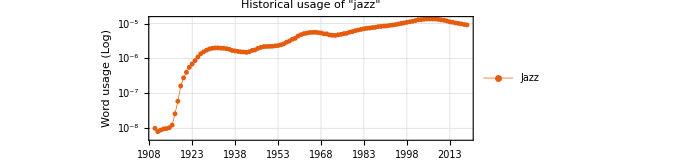

```mathematica
(* 10-yr moving average of word usage (case ignored) *)
```

```mathematica
(* connect to OpenLibrary API *)
openlibrary=ServiceConnect["OpenLibrary"];
(* func for getting book data *)
getBookData[title_]:=getBookData[title]=
```

```mathematica
(* titles *)
bookTitles=;
Panel@Labeled[Highlighted@Length@bookTitles,"No. of books from OpenLibrary API",Top]
(* publication dates *)
pubDates=;
MinMax@pubDates
```

7214No. of books from OpenLibrary API

{Year: 1899,Year: 2023}

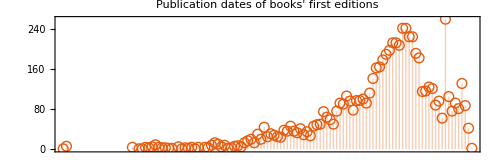

```mathematica
(* books' first publish dates (1st editions) *)
```

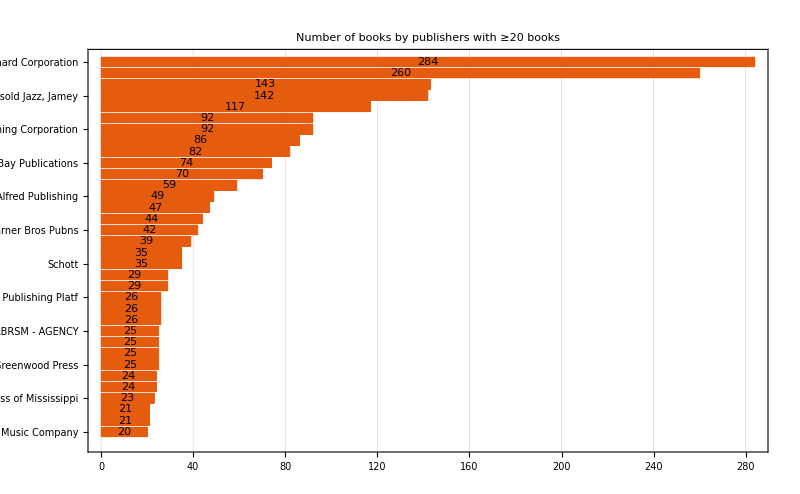

```mathematica
(* no. of books by each publisher (≥20 only) *)
```

```mathematica
(* plot freq of pub's & word use *)
```

-Graphics-Historical frequencies of book publications and word usage

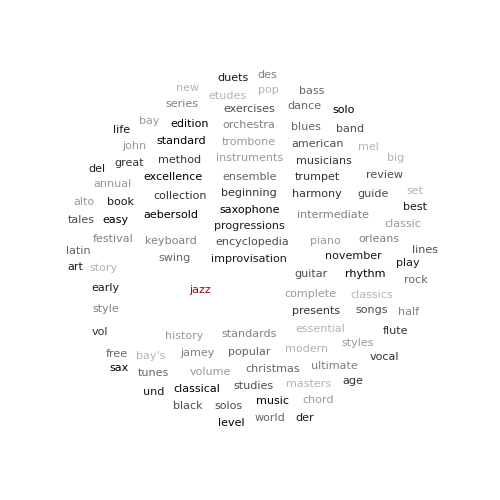
-Graphics- |  —  — jazz7335
 —  — guitar445
 —  — piano399
 —  — book278
 —  — mel217
 —  — blues217
 —  — vol216
 —  — standards203
 —  — music189
 —  — guide180
 —  — bay175
 —  — improvisation155
 —  — ensemble152
 —  — new151
 —  — age148
 —  — jamey136
 —  — aebersold134
 —  — solos117
 —  — history106
 —  — play96

```mathematica
(* wordcloud of book titles *)
```

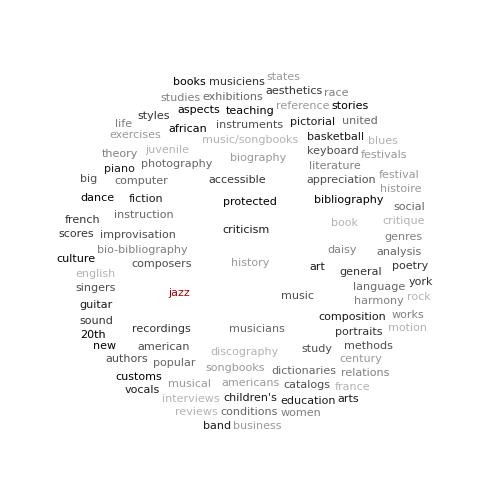
-Graphics- |  —  — jazz4021
 —  — music1672
 —  — history1518
 —  — criticism1348
 —  — musicians973
 —  — book959
 —  — accessible958
 —  — protected895
 —  — daisy895
 —  — study400
 —  — biography397
 —  — fiction382
 —  — instruction376
 —  — discography280
 —  — general261
 —  — literature220
 —  — african219
 —  — american218
 —  — musical196
 —  — piano189

```mathematica
(* wordcloud of book subjects *)
```

```mathematica
(* counts by author name *)
bookAuthorCounts=;
Select[bookAuthorCounts,#>10&]
```

<|Mark C. Gridley→32,Alfred Publishing→46,Paul Tanner→16,David W. Megill→15,Henry Martin→12,Hal Leonard Corp.→162,Nat Hentoff→14,Richard Cook→13,Leonard Feather→30,Jerry Coker→14,Dave Wolpe→15,Corey Christiansen→42,F. Scott Fitzgerald→30,Carolyn Graham→17,Bob Phillips→11,Randy Sabien→11,Ted Gioia→14,Dan Haerle→19,John Fordham→14,Jody Fisher→20,Martin T. Williams→13,Martin Williams→12,Hugues Panassié→16,Brent Edstrom→12,Lucien Malson→11,John O'Neill→12,Keith Shadwick→12,William Bay→11,Various→31,Hal Leonard Corp. Staff→37,David N. Baker→22,Lee Evans→19,Frank Mantooth→21,Eddie Condon→11,Martha Mier→24,Bill Boyd→17,Jamey Aebersold→89,David Baker→18,Mario Cerra→19,Ariel Ramos→19,mDecks Music→11,Mike Lewis→13,Jack Bullock→13,Ruby Morgan→18,Dean Sorenson and Bruce Pearson→11|>

```mathematica
(* convert keys to entities *)
mapped=ParallelMap[Interpreter["MusicAct"|"Person"][#[[1]]]->#[[2]]&,Normal[bookAuthorCounts],Method->"CoarsestGrained",ProgressReporting->True];
```

```mathematica
(* no.s of books by/accredited to musicians *)
booksByMusicians=ReverseSort@KeySelect[Association[mapped],!FailureQ[#1]&]
```

<|F. Scott Fitzgerald→30,Martha Mier→24,Jodie Fisher→20,Lee Evans→19,David J. Baker→18,Bill Boyd→17,Paul Tanner→16,John Fordham→14,Nat Hentoff→14,Mike Lewis→13,Martin T. Williams→13,John P. O'Neill→12,Henry Robert Martin→12,William Van Ness Bay→11,Bob Phillips→11,Joe Alexander→9,Geoffrey C. Ward→9,William Claxton→9,James Lincoln Collier→9,Duke Ellington→8,Herman Leonard→8,Oscar Peterson→8,Boris Vian→8,Tom Lord→8,Peter Francis Hammond→7,Richard O'Brien→7,Mark L. Taylor→7,Ken Burns→7,Wynton Marsalis→7,Keith Waters→7,Barney Kessel→6,Lee Tanner→6,John W. Griggs→6,Mark Levine→6,Julie Smith→6,Brian Priestley→6,Lewis Porter→6,Barry Ulanov→6,Jimmy Haslip→5,Horace Silver→5,Entity[MusicAct,Tedashii::33nky]→5,Dick Hyman→5,John LaPorta→5,Mel Bay→5,John Coltrane→5,Francis Davis→5,Dave Brubeck→5,James Stewart→5,Tony Esposito→5,Bill Lee→5,Ira Gitler→5,Philip Larkin→5,Brian Morton→5,Henri Matisse→5,Toni Morrison→5,Clifford Brown→4,Steve Davis→4,Bob Chilcott→4,Wes Montgomery→4,Miles Davis→4,Andrew Green→4,Mark Harrison→4,Sammy Stein→4,Lalo Schifrin→4,Dmitri Shostakovich→4,John Scofield→4,Buck Clayton→4,Eddie Harris→4,Billy Taylor→4,Tom Anderson→4,Vachel Lindsay→4,Joe Pass→4,Max Jones→4,Entity[Person,WalterDeanMyers::wv3gv]→4,Entity[MusicAct,RexStewart::yv9hz]→4,Kyle Lowder→4,Langston Hughes→4,Max Harrison→4,Ian Carr→4,Gary Giddins→4,James Ellroy→4,Kathy Ellis→3,Ted Greene→3,Sonny Rollins→3,Sean O'Leary→3,Alec Wilder→3,Doug Anderson→3,James M. Hall→3,Clark Collier→3,Charles Wood→3,Benny Goodman→3,Bill Cunliffe→3,Gary Dahl→3,Mark Hayes→3,Ronnie Lee→3,Charlie Byrd→3,Robert Crumb→3,Lil Jon→3,Howie Mandel→3,Charles L. Robinson→3,Jacob Coker→3,Bill Evans→3,Frank Driggs→3,Ethan Mordden→3,Mickey Baker→3,Danny Barker→3,Buddy Rich→3,Mike Steiner→3,Christopher Wilkinson→3,Al Rose→3,Marcel Pagnol→3,Edward S. Walker→2,Barry Long→2,Joe Bennett→2,Douglas MacArthur→2,Randy Brecker→2,David Hughes→2,John Webb→2,Count Basie→2,Jean Rhys→2,Ron Carter→2,Stan Getz→2,Bucky Pizzarelli→2,Guerino Mazzola→2,Paul Oliver→2,Chick Corea→2,Stefan Grossman→2,Herb Drury→2,Jack Mitchell→2,Linda Barker→2,Kenneth Baker→2,Ron Carter→2,Josef Škvorecký→2,Entity[Person,PierreBourque::6wfj4]→2,Michiel de Ruyter→2,Frank Obadiah Briggs→2,Boris Blacher→2,Billy Joel→2,John Berry→2,Dexter Gordon→2,Ring Lardner→2,Michael Anthony→2,Scott Miller→2,Woody Shaw→2,The Beatles→2,Malcolm Cowley→2,Cole Porter→2,Tal Farlow→2,Bobby Brown→2,Guido De Luigi→2,John O'Sullivan→2,Bob Willoughby→2,Elton John→2,Harley Race→2,Mike WiLL Made-It→2,Tom Dempsey→2,Giovanni→2,Drew Daniel→2,Dick Williams→2,Frank Sibley→2,Gary Campbell→2,Mark White→2,Michael Jacobs→2,Thelonious Monk→2,Carl Poole→2,Herb Ellis→2,Charles Fox→2,Bill Hart→2,Jay Friedman→2,Larry Carlton→2,John Robert Brown→2,George Gershwin→2,Hale Smith→2,Ken Mitchell→2,Charlie Parker→2,Daniel Pinkwater→2,Ray Avery→2,Paul Bearer→2,Mark Stewart→2,Christian Rose→2,Allen Carter→2,Dennis Taylor→2,Mike Springer→2,Hayden Carruth→2,Harvey Brown→2,John Lewis→2,Liz Jones→2,Cameron Walter→2,Eric Porter→2,Herbert Chappell→2,Yusef Komunyakaa→2,Andy McKee→2,Andrew Lloyd Webber→2,Andy Jones→2,Robert B. Gordon→2,Mary Morris→2,K.C. Kelly→2,David Houston→2,Dave Cutler→2,Mark Thomas→2,Albert White→2,Dennis Stock→2,Paul Whiteman→2,David Grayson→2,Johann Sebastian Bach→2,Charles Lewis Beale→2,Mike Zwerin→2,W. Eugene Smith→2,Francis Newton→2,Richard Byrd→2,Humphrey Lyttelton→2,Jazz Jennings→2,Bill Crow→2,Mary Hays Weik→2,Arnold Shaw→2,Marian McPartland→2,Orrin Keepnews→2,Tavis Smiley→1,Kevin Boyle→1,Hoagy Carmichael→1,George Antheil→1,Ted Reed→1,Larry Ross→1,Milt Hinton→1,Jimmy Wyble→1,Bob Coleman→1,Angela Smith, Baroness Smith of Basildon→1,James R. Campbell→1,Bob Weir→1,James Lovelock→1,CJ→1,Graydon Carter→1,Spencer Leigh→1,Skream→1,Jeanne Balibar→1,Alain Caron→1,Jerome Kern→1,Larry Anderson→1,Bobby Gordon→1,Frank Layden→1,John Zorn→1,George Wein→1,Mark Tucker→1,Charles Chapman→1,Lisa Arrindell Anderson→1,Billy Strayhorn→1,Mengistu Haile Mariam→1,Brown→1,Scott Henderson→1,Kevin Jackson→1,Bronson Pinchot→1,John Hancock→1,Frank Cordell→1,Doug Stone→1,Douglas F. Mackenzie→1,Greg Williamson→1,Michael Tucker→1,David James Elliott→1,David Sanborn→1,Jaco Pastorius→1,Duck Baker→1,Dave Smith→1,Django Reinhardt→1,Gregory Frost→1,Stuart Rawlins→1,Michael Welch→1,Pannonica de Koenigswarter→1,Tom Banks→1,David Marshall→1,Brian Austin Green→1,Dudu Topaz→1,David Delano Glover→1,Entity[Person,IsabelIce::4233q]→1,Entity[Person,BobWilber::78yf3]→1,Stan Kenton→1,Jerry Bergonzi→1,Freddie Hubbard→1,Cedar Walton→1,Benny Carter→1,Joe Henderson→1,Bobby Watson→1,Ludwig van Beethoven→1,Sidney Bechet→1,Lee Morgan→1,Cannonball Adderley→1,Jeff Daniels→1,Herbie Hancock→1,Allen Vizzutti→1,David Hamilton→1,Charlie Long→1,Andy Kirk→1,Sammy Price→1,Charlie Christian→1,Jana Kramer→1,Entity[Person,JosephCampbellButler::s2z62]→1,Roger Grove→1,Hal Smith→1,Domenico Scarlatti→1,Nathan Kennedy→1,Coleman Hawkins→1,Lewis Hill→1,William Orlando Smith→1,Graham Bell→1,Ben Hecht→1,Roger Guérin→1,A. L. Kennedy→1,Keith Mallett→1,André Previn→1,Petey Williams→1,Roy Porter→1,John Postgate→1,Bruce Johnson→1,Roger A. Thomas→1,Marvin Martin→1,Tom Rob Smith→1,Dave Marshall→1,Amiri Baraka→1,Patrick T. Harker→1,Mackie Jayson→1,Jonathan Hansen→1,Ben E. King→1,Jonathan Bernier→1,Mike Garson→1,William H. Swanson→1,Michael Cochrane→1,Lee P. Brown→1,Daisy Bates→1,Jim Carlton→1,Quincy Jones→1,Art Butler→1,David Schroder→1,Richard M. Miles→1,Alex Ebert→1,Dan Coats→1,Martin Cruz Smith→1,Charles-Eugène Delaunay→1,Tim Ferguson→1,Cedric Thompson→1,Leo Dillon→1,William Blount Carter→1,Pat Metheny→1,Mike Stern→1,Robben Ford→1,Steve Freeman→1,Norman Brown→1,John O'Reilly→1,Joe Elliott→1,John H. Beck→1,Case→1,Entity[Person,OtisFerguson::4v369]→1,Alexandra Wilson→1,James Tracy Hale→1,Gary Keller→1,Stevie Wonder→1,Alvin Ailey→1,Paul Farmer→1,Rob Garland→1,Ellie Harvie→1,Duke Ellington→1,Brian Winston→1,John McNeil→1,Stan Smith→1,Mike Hadlock→1,Bob Taylor→1,Paul Smith→1,Elizabeth Montgomery→1,Mark Walker→1,Martin Taylor→1,Bob Schultz→1,John Humphries→1,Claude Nougaro→1,Mary Lou Williams→1,Dave Thompson→1,Laurie Lewis→1,Arnold Perl→1,Ray Brown→1,Ornette Coleman→1,Vladimir Bogdanov→1,Jacinto Benavente→1,Tony Phillips→1,Mike Weaver→1,William A. Egan→1,Mike Paxton→1,Dizzy Gillespie→1,Blue Mitchell→1,Paolo Fresu→1,Michael Green→1,Django Reinhardt→1,Scott Wilson→1,Johnny Smith→1,Julio Coll→1,Joe Lovano→1,Michael Hoffman→1,Jayne Cortez→1,Nick Hornby→1,David Horn→1,Eavan Boland→1,Jay Thomas→1,Michael Wood→1,Ken Nordine→1,Doc Cheatham→1,Angélique Kidjo→1,Madeleine Peyroux→1,Eric Cantona→1,Jamie Cullum→1,George Benson→1,Lee Si-young→1,John Christensen→1,Al Capone→1,Gus Viseur→1,Paul Rankin→1,Tony Millionaire→1,John Jacob Riley→1,Henry Mancini→1,Bud Freeman→1,Pete Turner→1,Steve Harris→1,George Robert Stephenson→1,Colin King→1,Laurence James→1,Sandy Brown→1,Mel Brooks→1,Giuseppe Verdi→1,John Knowles→1,Throbbing Gristle→1,Chet Baker→1,Craig Copeland→1,Paul Barnes→1,Josef Horovitz→1,Ralph Hughes→1,Juan Antonio Arguelles Rius→1,James P. Johnson→1,Mark Cosgrove→1,Bix Beiderbecke→1,Hunter Hayes→1,Paul Desmond→1,Robert Alan Aurthur→1,Al Lerner→1,Marilyn Hacker→1,Mike Bethel→1,James Prior→1,Haruki Murakami→1,Antonio Carlos Jobim→1,Bryan White→1,Ray Collins→1,Mike Barnes→1,Neil Diamond→1,Peter Westbrook→1,Robert Penn Warren→1,Mohammed Dib→1,Jerry Snyder→1,Jack Vance→1,Robert I→1,Bob Patterson→1,John Michael Montgomery→1,Frank E. Evans→1,Norman Granz→1,Entity[Person,Metacom::2cj5c]→1,Scott DeVeaux→1,Oscar Pettiford→1,David Hyde Pierce→1,Johnny Wilson→1,William Lee→1,Pete Townshend→1,Chris Barber→1,Stanley Green→1,Edmund Wilson→1,Clint Eastwood→1,Mark Crispin Miller→1,Frances Newton→1,Mel Greig→1,Art Blakey→1,Bob Fosse→1,The Dave Brubeck Quartet→1,Jay Arnold→1,Jelly Roll Morton→1,Lee So-ra→1,George Benson→1,James Tate→1,Buddy Collette→1,Joe Morello→1,Jorge Guinle→1,Bruce Clarke→1,Paul Harvey→1,Matt Glaser→1,Nicolas Evans→1,Bob Porter→1,Tracy Ryan→1,John Rowe→1,David Peterson→1,Bill Smith→1,Charles Eaton Haynes→1,Paolo Gennari→1,Joe Darensbourg→1,David Butler→1,Ian Rankin→1,Bob Rusch→1,Gene Krupa→1,Ezekiel Honig→1,Cheryl→1,Julio González→1,Robert Wolf→1,Kōsō Abe→1,Dean Kelly→1,Johannes Brahms→1,Maurice Jackson→1,Richard C. Hunter→1,Clutch→1,Geoff Dyer→1,Carlos Andrés Pérez→1,Jorge García→1,Janelle Monáe→1,Bill Lee→1,Roger→1,Mike Kennedy→1,David Baldwin→1,David Janssen→1,Michael Gerber→1,Jacques Sadoul→1,Ann Miller→1,Bryan Knight→1,John Murray→1,Bernard Heuvelmans→1,Wayne Shorter→1,Harry Dial→1,Bob Allen→1,James Emanuel→1,Paul Wendkos→1,George Collier→1,John Scott Russell→1,William Odom→1,Ted Williams→1,John Wilson→1,J.J. Johnson→1,Dick Hermann→1,Little Milton→1,David Sharp→1,Stephen Longstreet→1,Lee Friedlander→1,Lars Løkke Rasmussen→1,Charles Alexander→1,Art Kane→1,Artie Shaw→1,Teddy Wilson→1,Barbara Lea→1,Alan Phillips→1,Allan Rich→1,Igor Stravinsky→1,Jeremy Brown→1,John Ryan→1,Richard Woodley→1,William E. Miller→1,Jonny King→1,Kathy Baker→1,christ.→1,John Dankworth→1,Jeff Wills→1,Bob Brunning→1,Stephen Harrison→1,William T. Sherman→1,Raul Fernandez→1,Ray Smith→1,Entity[Person,KevinYoung::r795k]→1,Peter Ind→1,Leonard Bernstein→1,John Storm Roberts→1,Tim Berry→1,Edward Lee→1,Mark Brown→1,John Romita, Sr.→1,Roy Thomas→1,John Romita Jr.→1,Tony Wilson→1,London Philharmonic Orchestra→1,Andrew Charlton→1,Adam Levy→1,Brian Rust→1,Michael Alexander→1,Abraham→1,Jeff A. Schwartz→1,Virgil Suárez→1,Ben Sidran→1,Gregory Clark→1,Mike Sweeney→1,Robert Gottlieb→1,Floyd Levin→1,Donald Miller→1,Diana Abu-Jaber→1,Gene Lees→1,Eric Hobsbawm→1,Rick Cook→1,Jeff Coffin→1,Caleb Chapman→1,Studs Terkel→1|>

## Jazz musicians

The Wikipedia page "List of jazz musicians" contains a list of musicians for which there a Wikipedia article exist. Conveniently, the musicians are grouped by instruments. Some instrument categories are listed here, while others linked to a separate Wikipedia page of list for that particular instrument.

To get the other lists, we can get all links in the current article (“List of jazz musicians”) and parse it and extract links that are likely to be instrument-specific (e.g., containing ‘List of,’ and ending with ‘ists’ [instrument] or ‘musicians’ [genre]). It’s worth taking a look at the category page "Category:Lists of jazz musicians" too. There are many sub-genres of Jazz and certainly many more different types of instruments involved. I will only focus on some and not all of these.

```mathematica
(* get articles with lists *)
listArticleTitles=
```

{List of bebop musicians,List of chamber jazz musicians,List of cool jazz and West Coast jazz musicians,List of hard bop musicians,List of jazz banjoists,List of jazz bassists,List of jazz fusion musicians,List of jazz guitarists,List of jazz organists,List of jazz percussionists,List of jazz pianists,List of jazz saxophonists,List of jazz trombonists,List of jazz vibraphonists,List of jazz violinists,List of jazz vocalists,List of smooth jazz musicians,List of soul jazz musicians,List of swing musicians,List of vibraphonists}

Those are the links to other lists. As for the musicians listed on this list, we need to do some parsing to extract them:

```mathematica
(* get article -> parse to paragraphs -> drop headings w/ links -> split strings @ new lines *)
parsedLists=;
(* display lists grouped by instrument *)

(* alternative display *)
;
```

Instrument | Examples | No. of Musicians
Accordion | , , Kamil Běhounek (1916–1983)Luciano Biondini (born 1971)Asmund Bjørken (1933–2018)Stian Carstensen (born 1971) | 18
Bass guitar | , , Victor Bailey (1960–2016)Brian Bromberg (born 1960)Stanley Clarke (born 1951)Bob Cranshaw (1932–2016) | 15
Bassoon | , , Garvin Bushell (1902–1991)Karen Borca (born 1948)Yusef Lateef (1920–2013)Illinois Jacquet (1922–2014) | 7
Cello | , , Harry Babasin (1921–1988)Ron Carter (born 1937)David Darling (born 1941)Richard Davis (born 1930) | 16
Clarinet | , , Woody Allen (born 1935)Craig BallBarney Bigard (1906–1980)Don Burrows (1928–2020) | 31
Cornet | , , Nat Adderley (1931–2000)Louis Armstrong (1901–1971)Bix Beiderbecke (1903–1931)Buddy Bolden (1877–1931) | 12
Flugelhorn | , , Joe Bishop (1907–1976)Art Farmer (1928–1999)Freddie Hubbard (1938–2008)Thad Jones (1923–1986) | 8
Flute | , , Greg Abate (born 1947)Jane Bunnett (born 1956)Wayman Carver (1905–1967)Buddy Collette (1921–2010) | 31
French horn | , , David Amram (born 1930)Vincent Chancey (born 1950)John Clark (born 1944)Junior Collins (1927–1976) | 11
Harmonica | , , Larry Adler (1914–2001)William Galison (born 1958)Max Geldray (1916–2004)Howard Levy (born 1951) | 8
Harp | , , Dorothy Ashby (1932–1986)Alice Coltrane (1937–2007)Adele Girard (1913–1993)Corky Hale (born 1936) | 6
Miscellaneous | , , Rufus Harley – bagpipesMeade Lux Lewis – celesteEmmett Chapman – Chapman stickRed McKenzie – comb | 22
Oboe | , , Bob Cooper (1925–1993)Yusef Lateef (1920–2013)Paul McCandless (born 1947)Makanda Ken McIntyre (1931–2001) | 6
Tuba | , , Bill Barber (1920–2007)Pete Briggs (1904–unknown)Don Butterfield (1923–2006)Red Callender (1916–1992) | 12

We’ll convert each name to a proper music act or person entity. To do this, we’ll first parse out the names from each Wikipedia page (e.g., “List of soul jazz musicians”), and then convert the names to a musical act—or a person if there’s no such interpretation found. 

Perhaps only the more popular musicians will have a curated entity record. That’s fine. We should still get enough information to do a meaningful exploration of Jazz musicians.

```mathematica
(* map symbols to entities *)
(* get symbol names with: (ToExpression["Musicians"<>StringTrim@StringDelete[#,"="|" "]]&/@parsedLists[[;;,1]]) *)
=;
```

Now, let’s get the other lists. These pages have the musicians listed as links, instead of plaintext names like before. Extracting either plaintext or list before parsing doesn’t work as well combining the parses of both, hence the Union in the extractEntities function. Highly inefficient, but necessary, at least for now. 

I also figured out that some of the artists appear in multiple lists, so we’ll convert a given plaintext name to an Entity just once and save that result, in case we come across it elsewhere. This will save some time by preventing multiple conversions of the same string.

```mathematica
(* get article -> parse to paragraphs -> drop headings w/ links -> split strings @ new lines -> delete string after hyphen*)
parseList2[articleTitle_]:=;
```

```mathematica
(* convert list of names to proper entities (use memoization for speed) *)
listToEntities[names_]:=listToEntities[names]=;
(* extract likely artist/person entities from a Wikipedia page *)
extractEntities[wikipage_]:=
```

```mathematica
(* by instrument *)
```

```mathematica
(* by sub-genre *)
```

```mathematica
(* other *)
```

Having scoured Wikipedia for names of Jazz musicians, we can put all this information into a single list. Note that: 
1. This is not a comprehensive list of all Jazz musicians in the world, but rather (a subset of interpretable names within) a subset of the names found on some Wikipedia articles on Jazz. It’s far from comprehensive. 2. There are definitely some name-to-entity misinterpretations, too. Hopefully not too many. One way to minimise this could be to increase the acceptance threshold of the NER algorithm. But by doing so, it may inadvertently misinterpret a well-known artist whose name is uncommon.
3. There most probably are better ways to get this data. Besides using WikipediaData like we did, one can use the Import function to XML of wiki pages and parse them.

```mathematica
allMusicians=Sort@DeleteDuplicates@Flatten[{(* instruments *)MusiciansAccordion,MusiciansBassguitar,MusiciansBassoon,MusiciansCello,MusiciansClarinet,MusiciansCornet,MusiciansFlugelhorn,MusiciansFlute,MusiciansFrenchhorn,MusiciansHarmonica,MusiciansHarp,MusiciansMiscellaneous,MusiciansOboe,MusiciansTuba,MusiciansBanjo,MusiciansGuitar,MusiciansOrgan,MusiciansPercussion,MusiciansPiano,MusiciansSaxophone,MusiciansTrumpet,MusiciansTrombone,MusiciansVibraphone,MusiciansViolin,MusiciansDrums,MusiciansVocals,(* sub-genres *)MusiciansBebop,MusiciansHardBop,MusiciansSmooth,MusiciansSoul,MusiciansSwing,MusiciansChamber,MusiciansCoolAndWestCoast,MusiciansFusion ,(* other *)MusiciansMen,MusiciansWomen}];
```

```mathematica
(* total # of musicians *)
Highlighted@Length@allMusicians
```

1495

## Albums and tracks

```mathematica
(* properties of an artist *)
EntityProperties["MusicAct"]
```

{albums,country,end date,image,members,members and dates,name,place of origin,start date,works}

```mathematica
(* example artist dataset *)
Entity["MusicAct","JohnColtrane::v78w2"]["Dataset"]
```

```mathematica
(* properties of albums *)
EntityProperties["MusicAlbum"]
```

{label,tracklist,number of discs,number of songs,canonical release,release date,runtime,image,artist,type,name,releases}

```mathematica
(* example album dataset *)
Entity["MusicAlbum","GiantSteps::d24z6"]["Dataset"]
```

```mathematica
(* properties of recordings/tracks *)
EntityProperties["MusicWorkRecording"]
```

{composer,length,music work,name,music act,albums,first release date}

```mathematica
(* example recording dataset *)
Entity["MusicWorkRecording","Naima::3mmxb"]["Dataset"]
```

```mathematica
images1=With[{albums=Entity["MusicAct","JohnColtrane::v78w2"]["Albums"]},
DeleteMissing[#[EntityProperty["MusicAlbum","Image"]]&/@albums]];
```

```mathematica
ImageCollage[images1,ImageSize->500]
```

-Graphics-

```mathematica
FeatureSpacePlot[images,FeatureExtractor->({Mean[ImageData[#]],DominantColors[#1,1]}&)]
```

-Graphics-

FeatureSpacePlot[images,FeatureExtractor→({Mean[ImageData[#1]],DominantColors[#1,1]}&)]